# Modular Arithmetic

## Use Modular Arithmetic to “cycle through the Colors”

REFERENCE (Jill Britton): 
http://maxwelldemon.com/2011/11/20/22-1-patterns-in-modular-arithmetic/

## Make a List of Colors

```mathematica
colorLIST = { Red, Orange, Yellow, Green, Blue, Magenta, Purple };
```

## Print a Row of Dots

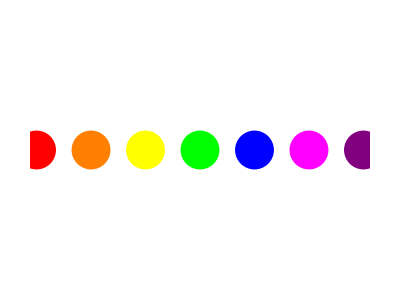

```mathematica
Graphics[{
		PointSize[0.07],
		Table[ {
				colorLIST[[i]],                   (* Pick Color i *)
				Point[{i,0}]                          (* Draw it at this Point*)
			  }, 
			{i,1,Length[colorLIST]} ]         (* Count from 1 to 7 *)
	}]
```

## Multiple Rows of the same colors

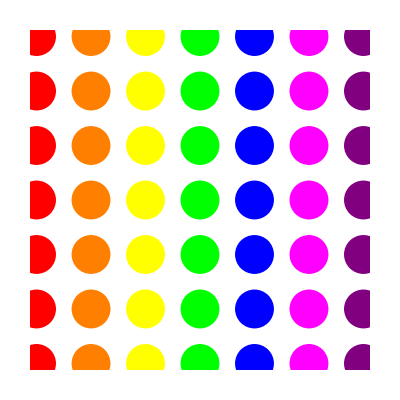

```mathematica
Graphics[{
		PointSize[0.07],
		Table[{
				 colorLIST[[i]], 
				Point[{i,j}]                        (* Draw at this point *)
			}, 
		{i,1,Length[colorLIST] },                (* Count columns 1 to 7 *)
		{j, 1, Length[colorLIST]}                   (* Count rows 1 to 7 *)
		 ]
	}]
```

## Modding Along Each row -- Add Row Number + Column Number

Remark :   Mod[ i+j, 7, 1]
		   Mod[ i+j, Length[colorLIST], 1]
   says 
            add i+j
            Mod the answer by 7.
            Don’t use 0:  
                So the numbers are 
                	1,2,3,4,5,6,7
                instead of 
                	0,1,2,3,4,5,6

### Illustrate Mod

#### "Style" just to make the output larger

```mathematica
Table[
	   Style[  i    , FontSize-> 24],
	{i,1, 15}
      ]

Table[
	   Style[    Mod[i,12,1], FontSize-> 24],
	{i,1, 15}
]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

{1,2,3,4,5,6,7,8,9,10,11,12,1,2,3}

### Graphing

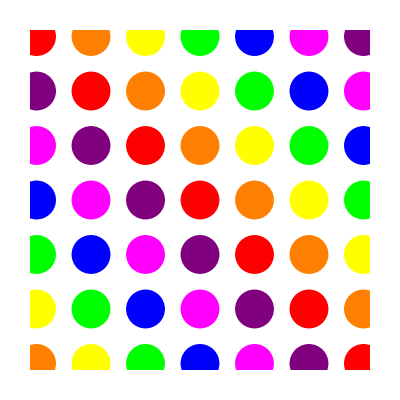

```mathematica
Graphics[{
		PointSize[0.07],
		Table[{ 
				colorLIST[[    Mod[i+j,Length[colorLIST],1]   ]],      
										(* Modding - see remark *)
				Point[{i,j}]
			}, 
			{i,1,Length[colorLIST]},
			{j, 1, Length[colorLIST]}
		       ]
	}]
```

### Change the SIZE of the ARRAY

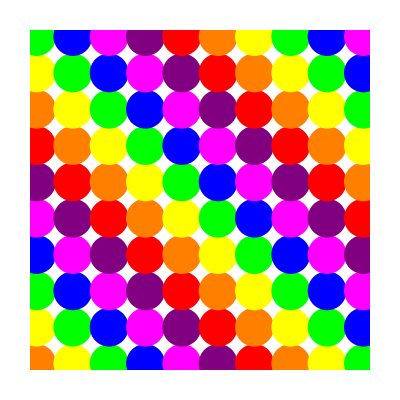

```mathematica
SIZE = 10;                            (* try other Numbers *)

Graphics[{
		PointSize[0.07],
		Table[       { colorLIST[[Mod[i+j,Length[colorLIST],1]]], Point[{i,j}]}, 
			{i,1,SIZE},
			{j, 1, SIZE}                                (* Use New SIZE *)
		 ]
	}]
```

### A Row of Triangles

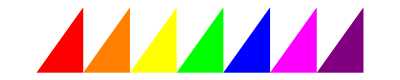

```mathematica
Graphics[{
		Table[
				{  colorLIST[[i]], 
				 Polygon[{
						{i,0}, {i+1,0},{i+1,1}
					}]
				},
				{i,1, Length[colorLIST]}
			]
	}]
```

### A Row of Squares

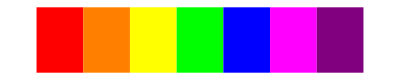

```mathematica
Graphics[{
		Table[
				{  colorLIST[[i]], 
				 Polygon[{
						{i,0}, {i+1,0},{i+1,1}, {i, 1}
					}]
				},
				{i,1, Length[colorLIST]}
			]
	}]
```

### An Array of Squares

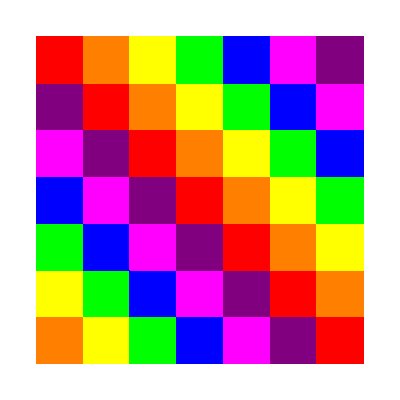

```mathematica
SIZE = 7;

Graphics[{
		Table[
				{  colorLIST[[    Mod[i+j, Length[colorLIST], 1]   ]], 
				 Polygon[{
						{i,j}, {i+1,j},{i+1,j+1}, {i, j+1}
					}]
				},
				{i,1, SIZE},
				{j, 1, SIZE}
			]
	}]
```

### Scaling -- Color Boxes

Explanation :
	Scale[  image,  {x-factor, yfactor}, cornerToScaleTo ]   <-- using corner = {0,1}
	 								scales to left
	 								scales to top
	 Translate[image, {x-translate, y-translate} ]
	 	First box starts at x=0 and is .9^0 = 1 wide.
	 	Second box starts .9^0 = 1  and is .9^1 wide
	 	Third box starts at .9^0+.9^1 and .9^2 wide
	 	Fourth box starts at .9^0+.9^1+.9^2 and is .9^3 wide
	 	... back to first box. get start = 0 by Sum[ ..., {k,0,-1}]  <-- no sum -- it gives 0
	 	
	Diresssion: Translate is { x, -y }   <-- “-“ because I imagine rows going down.

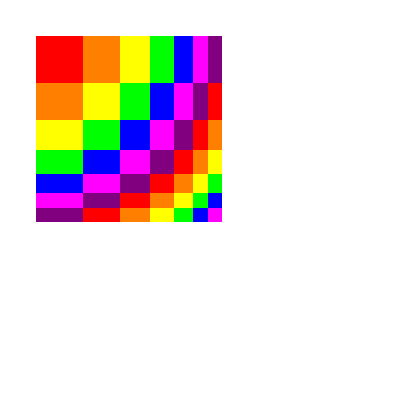

```mathematica
SIZE = 6;
scaleBY = .8;
Graphics[{colorArray=
		Table[{  
			colorLIST[[    Mod[i+1+j, Length[colorLIST], 1]   ]], 
			Translate[
					  Scale[ 
						    Polygon[{     {0,0},{1,0},{1,1},{0,1}   }],
						   {scaleBY^i, scaleBY^j},{0,1}
						],
					{Sum[(scaleBY)^k,{k,0,i-1}],-Sum[(scaleBY)^k,{k,0,j-1}]}
					]
			},
			{i,0, SIZE},
			{j, 0,SIZE}
			]
	},PlotRange-> {  {0,SIZE+1}, {-SIZE,1} }]
```

## SuperTile of Scaling Color Boxes

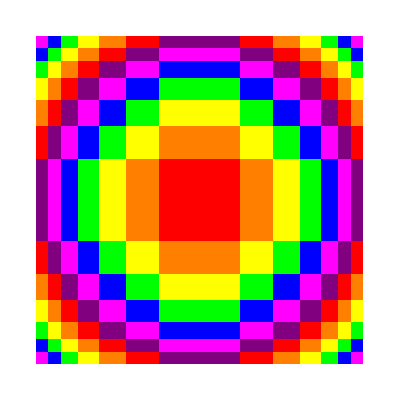

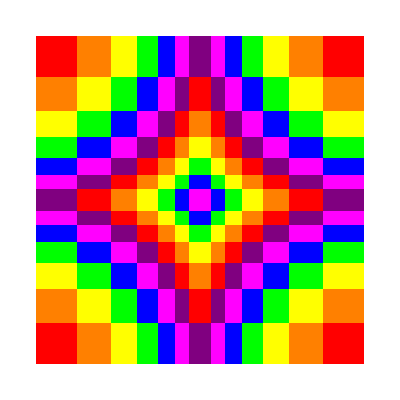

```mathematica
widthHeight = Sum[(scaleBY)^k,{k,0,SIZE}];

reflectV = GeometricTransformation[ colorArray, 
			ReflectionTransform[{1,0}, {0,0}]];
reflectH = GeometricTransformation[ colorArray, 
			ReflectionTransform[{0,1}, {0,1}]];
rotate = GeometricTransformation[ colorArray, 
			RotationTransform[Pi, {0,1}]];

Graphics[ { rotate,reflectH, colorArray, reflectV,
} ]


Graphics[ {colorArray,
Translate[reflectV, {2*widthHeight,0} ],
Translate[reflectH, {0, -2*widthHeight} ],
Translate[ rotate, {2*widthHeight,-2*widthHeight}]

}]
```

## Scaling -- Color Boxes ADDED Axes and Corner Point at {0,0}

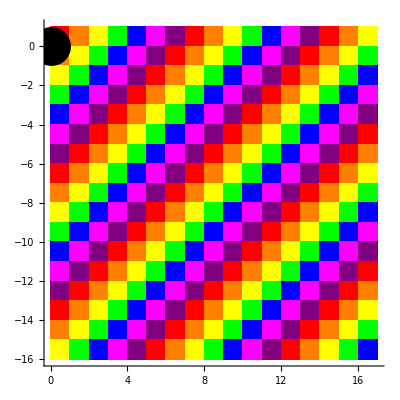

```mathematica
SIZE = 16;
scaleBY = 1;
Graphics[{
		Table[{  
			colorLIST[[    Mod[i+1+j, Length[colorLIST], 1]   ]], 
			Translate[
					  Scale[ 
						    Polygon[{     {0,0},{1,0},{1,1},{0,1}   }],
						   {scaleBY^i, scaleBY^j},{0,1}
						],
					{Sum[(scaleBY)^k,{k,0,i-1}],-Sum[(scaleBY)^k,{k,0,j-1}]}
					]
			},
			{i,0, SIZE},
			{j, 0,SIZE}
			],
PointSize[0.07],Point[{0,0}]
	},  Axes-> True, PlotRange-> {  {0,SIZE+1}, {-SIZE,1} }]
```

## Illustrating Different Functions with Mod

### Set a List of 7 Colors

```mathematica
colorLIST = { Red, Orange, Yellow, Green, Blue, Magenta, Purple };
```

### Row of - 7 Colors

```mathematica
(* A Row of Squares *)
Graphics[{
		Table[
				{  colorLIST[[i]], 
				 Polygon[{
						{i,0}, {i+1,0},{i+1,1}, {i, 1}
					}]
				},
				{i,1, Length[colorLIST] }
			]
	}]
```

-Graphics-

## Large Array - 7 Colors x + y Mod 7

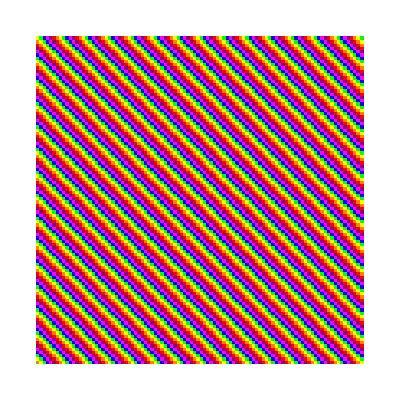

```mathematica
SIZE = 100;

Graphics[{
		Table[
				{  colorLIST[[    Mod[i+j, Length[colorLIST], 1]   ]], 
				 Polygon[{
						{i,j}, {i+1,j},{i+1,j+1}, {i, j+1}
					}]
				},
				{i,1, SIZE},
				{j, 1, SIZE}
			]
	}]
```

## Large Array - 7 Colors x * y Mod 7

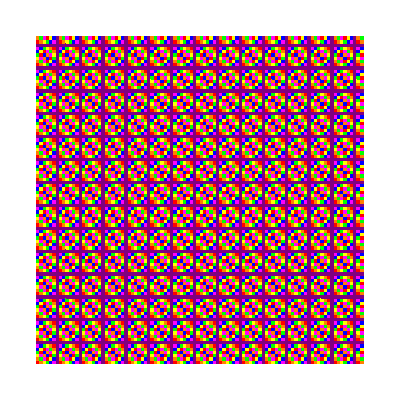

```mathematica
SIZE = 100;

Graphics[{
		Table[
				{  colorLIST[[    Mod[i*j, Length[colorLIST], 1]   ]], 
				 Polygon[{
						{i,j}, {i+1,j},{i+1,j+1}, {i, j+1}
					}]
				},
				{i,1, SIZE},
				{j, 1, SIZE}
			]
	}]
```

## Large Array - 7 Colors x^2 + y^2 Mod 7

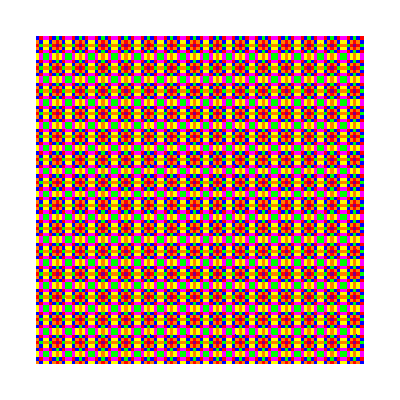

```mathematica
SIZE = 100;

Graphics[{
		Table[
				{  colorLIST[[    Mod[i^2+j^2, Length[colorLIST], 1]   ]], 
				 Polygon[{
						{i,j}, {i+1,j},{i+1,j+1}, {i, j+1}
					}]
				},
				{i,1, SIZE},
				{j, 1, SIZE}
			]
	}]
```

## Large Array - 7 Colors x^2 - y^2 + 3 x*y Mod 7

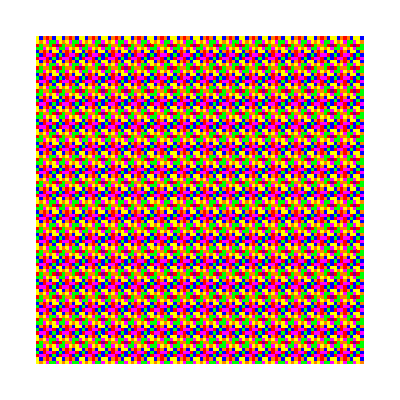

```mathematica
SIZE = 100;

Graphics[{
		Table[
				{  colorLIST[[    Mod[i^2-j^2 + 3 * i * j, Length[colorLIST], 1]   ]], 
				 Polygon[{
						{i,j}, {i+1,j},{i+1,j+1}, {i, j+1}
					}]
				},
				{i,1, SIZE},
				{j, 1, SIZE}
			]
	}]
```

## Multiple Colors Using Hue[]

Hue(x)
         As hx varies from 0 to 1, t
         the color corresponding to Hue[h] 
         runs through 
         red, yellow, green, cyan, blue, magenta, and back to red again

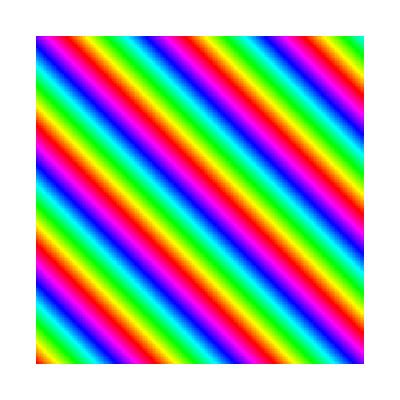

```mathematica
numberOfColors = 73;

colors = Table[  Hue[ i/numberOfColors], {i,1, numberOfColors} ];

Graphics[{			
		     Table[ {colors[[  Mod[x+y,numberOfColors,1] ]], 
				Rectangle[ {x,y},{x+1,y+1}]},
		{x,0,200},{y,0,200}]
}]
```

## Multiple Colors RGB[ {r,g,b} ]

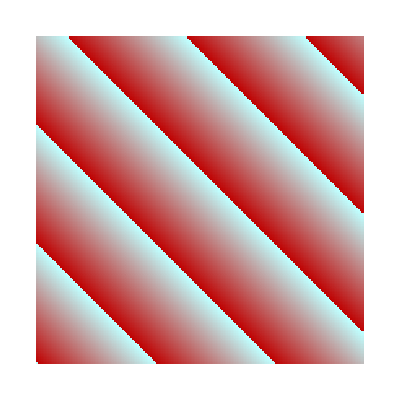

```mathematica
numberOfColors = 73;

colors = Table[  RGBColor[ 0.75, i/numberOfColors, i/numberOfColors], {i,1, numberOfColors} ];

Graphics[{
	Table[ {colors[[  Mod[x+y,numberOfColors,1] ]],
			Rectangle[ {x,y},{x+1,y+1}]},
					{x,0,200},{y,0,200}]
}]
```

## Boxes inside Boxes

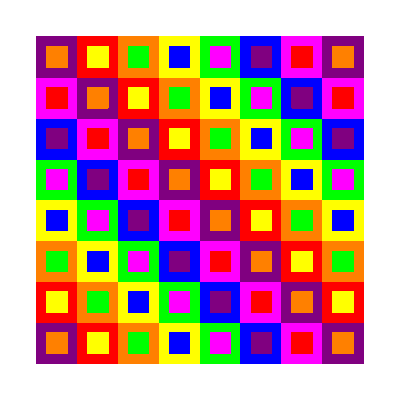

```mathematica
Graphics[{
			(* Outside Rectangle *)
	Table[{
		 colorLIST[[   Mod [x+y, Length[colorLIST],1]  ]], 
			Rectangle[ {x,y},{x+1,y+1}]
		}, 
		{x,0,7},
		{y,0,7}],

			(* Inside Rectangle *)
	Table[{
		 colorLIST[[   Mod [x+y+2, Length[colorLIST],1]  ]], 
		Rectangle[ {x+0.25,y+0.25},{x+0.75,y+0.75}]
		}, {x,0,Length[colorLIST]},{y,0,Length[colorLIST]}]
	}]
```

## Boxes inside Boxes - Randomizing

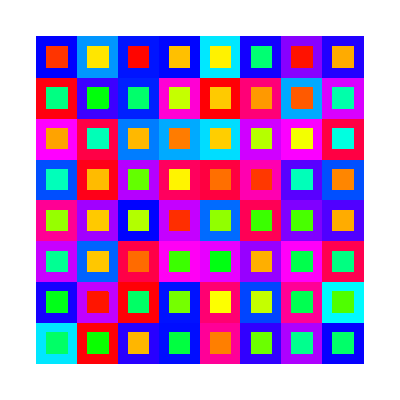

```mathematica
(* Random Colors *)

Graphics[{
			(* Outside Rectangle *)
	Table[{
		 Hue[ RandomReal[]/2 + 1/2], 
			Rectangle[ {x,y},{x+1,y+1}]
		}, 
		{x,0,7},
		{y,0,7}],

			(* Inside Rectangle *)
	Table[{
		 Hue[ RandomReal[]/2], 
		Rectangle[ {x+0.25,y+0.25},{x+0.75,y+0.75}]
		}, {x,0,7},{y,0,7}]
	}]
```

### Same with RGBColor

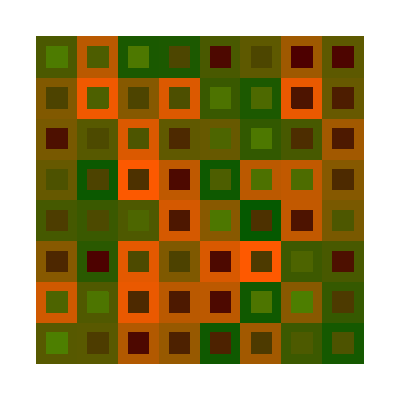

```mathematica
(* Random Colors *)

Graphics[{
			(* Outside Rectangle *)
	Table[{

		RGBColor[{   RandomReal[], 0.35, 0 }], 
			Rectangle[ {x,y},{x+1,y+1}]
		}, 
		{x,0,7},
		{y,0,7}],

			(* Inside Rectangle *)
	Table[{
		 RGBColor[{   0.3, RandomReal[], 0}],
		Rectangle[ {x+0.25,y+0.25},{x+0.75,y+0.75}]
		}, {x,0,7},{y,0,7}]
	}]
```

## 3 colors in Hue

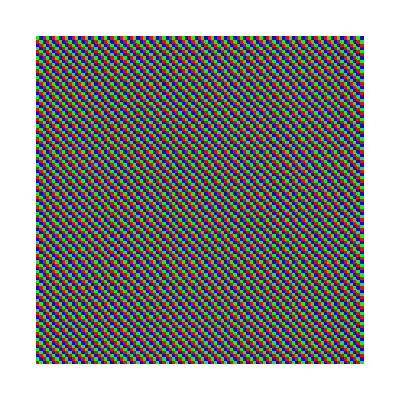

```mathematica
numberOfColors = 3;

colors = Table[  Hue[ i/numberOfColors], {i,1, numberOfColors} ];

Graphics[{

			Table[ {colors[[  Mod[x+y,numberOfColors,1] ]], Rectangle[ {x,y},{x+1,y+1}]},
					{x,0,100},{y,0,100}]
}]
```